```mathematica
E2a[n_,k_, a_]:= E2a[n,k,a]=Sum[ E2a[n/j,k-1,a],{j,2,n}]-a Sum[ E2a[n/(a j),k-1,a],{j,1,n/a}];E2a[n_,0,a_]:=1
EE[n_,z_,b_]:=EE[n,z,b]=Sum[FactorialPower[z,a]/a! E2a[n,a,b],{a,0,Log[If[b>2,2,b],n]}]
EEa[n_,z_,b_]:=EEa[n,z,b]=Sum[Binomial[z,a] E2a[n,a,b],{a,0,Log[If[b>2,2,b],n]}]
bins[ z_, a_] := Product[ (z-k),{k,0,a-1}]/a!
bins2[ z_, a_] := Product[ (z-k),{k,1,a-1}]/a!
EEb[n_,z_,b_]:=EEb[n,z,b]=Sum[bins[z,a] E2a[n,a,b],{a,0,Log[If[b>2,2,b],n]}]
EEc[n_,z_,b_]:=Expand[Sum[bins[z,a] E2a[n,a,b],{a,0,Log[If[b>2,2,b],n]}]]
gg[n_,z_,b_] := Expand[FullSimplify[(EEc[n,z+1,b]-1)/(z+1)]]
```

```mathematica
EE[100,z,2]
```

1-z+3/2 FactorialPower[z,2]-2/3 FactorialPower[z,3]-1/3 FactorialPower[z,4]+3/40 FactorialPower[z,5]-1/144 FactorialPower[z,6]

```mathematica
EEa[100,z,2]
```

1-z+3/2 (-1+z) z-2/3 (-2+z) (-1+z) z-1/3 (-3+z) (-2+z) (-1+z) z+3/40 (-4+z) (-3+z) (-2+z) (-1+z) z-5 Binomial[z,6]

```mathematica
EEb[100,z,2]
```

1-z+3/2 (-1+z) z-2/3 (-2+z) (-1+z) z-1/3 (-3+z) (-2+z) (-1+z) z+3/40 (-4+z) (-3+z) (-2+z) (-1+z) z-1/144 (-5+z) (-4+z) (-3+z) (-2+z) (-1+z) z

```mathematica
EEc[100,z,2]
```

1+(4 z)/5-(419 z^2)/72+(265 z^3)/48-(241 z^4)/144+(43 z^5)/240-z^6/144

```mathematica
Limit[( EE[100,z,2]-1)/z,{z->0}]
```

{4/5}

```mathematica
f[z_] := 1+(4 z)/5-(419 z^2)/72+(265 z^3)/48-(241 z^4)/144+(43 z^5)/240-z^6/144
```

```mathematica
Limit[(f[z]-1)/z,{z->0}]
```

{4/5}

```mathematica
Table[{n,Expand[Roots[EEc[n,x,2]==0,x]]},{n,2,40}]//TableForm
```

2 | x==1
3 | False
4 | x==1||x==2
5 | x==1/2-(ⅈ √7)/2||x==1/2+(ⅈ √7)/2
6 | x==-2||x==1
7 | x==-1||x==2
8 | x==1||x==2||x==3
9 | x==3+1/3 (486-3 √5667)^(1/3)+(162+√5667)^(1/3)/3^(2/3)||x==3-1/6 (486-3 √5667)^(1/3)-(ⅈ (486-3 √5667)^(1/3))/(2 √3)-(162+√5667)^(1/3)/(2 3^(2/3))+(ⅈ (162+√5667)^(1/3))/(2 3^(1/6))||x==3-1/6 (486-3 √5667)^(1/3)+(ⅈ (486-3 √5667)^(1/3))/(2 √3)-(162+√5667)^(1/3)/(2 3^(2/3))-(ⅈ (162+√5667)^(1/3))/(2 3^(1/6))
10 | x==1-ⅈ √5||x==1+ⅈ √5||x==1
11 | x==ⅈ √2||x==-ⅈ √2||x==3
12 | x==-1||x==1||x==3
13 | x==1-(2/(3 (27-√717)))^(1/3)-(1/2 (27-√717))^(1/3)/3^(2/3)||x==1+(1/2 (27-√717))^(1/3)/(2 3^(2/3))+1/(2^(2/3) 3^(1/3) (27-√717)^(1/3))-(ⅈ 3^(1/6))/(2^(2/3) (27-√717)^(1/3))+(ⅈ (27-√717)^(1/3))/(2 2^(1/3) 3^(1/6))||x==1+(1/2 (27-√717))^(1/3)/(2 3^(2/3))+1/(2^(2/3) 3^(1/3) (27-√717)^(1/3))+(ⅈ 3^(1/6))/(2^(2/3) (27-√717)^(1/3))-(ⅈ (27-√717)^(1/3))/(2 2^(1/3) 3^(1/6))
14 | x==5/2-(√37)/2||x==5/2+(√37)/2||x==1
15 | x==1-(2/(3 (27-√717)))^(1/3)-(1/2 (27-√717))^(1/3)/3^(2/3)||x==1+(1/2 (27-√717))^(1/3)/(2 3^(2/3))+1/(2^(2/3) 3^(1/3) (27-√717)^(1/3))-(ⅈ 3^(1/6))/(2^(2/3) (27-√717)^(1/3))+(ⅈ (27-√717)^(1/3))/(2 2^(1/3) 3^(1/6))||x==1+(1/2 (27-√717))^(1/3)/(2 3^(2/3))+1/(2^(2/3) 3^(1/3) (27-√717)^(1/3))+(ⅈ 3^(1/6))/(2^(2/3) (27-√717)^(1/3))-(ⅈ (27-√717)^(1/3))/(2 2^(1/3) 3^(1/6))
16 | x==3-23/(3^(1/3) (-324+√141477)^(1/3))+(-324+√141477)^(1/3)/3^(2/3)||x==3+23/(2 3^(1/3) (-324+√141477)^(1/3))-(23 ⅈ 3^(1/6))/(2 (-324+√141477)^(1/3))-(-324+√141477)^(1/3)/(2 3^(2/3))-(ⅈ (-324+√141477)^(1/3))/(2 3^(1/6))||x==3+23/(2 3^(1/3) (-324+√141477)^(1/3))+(23 ⅈ 3^(1/6))/(2 (-324+√141477)^(1/3))-(-324+√141477)^(1/3)/(2 3^(2/3))+(ⅈ (-324+√141477)^(1/3))/(2 3^(1/6))||x==1
17 | x==5/2+1/2 √(1/3 (-43+2269/(87803+90 ⅈ √490403)^(1/3)+(87803+90 ⅈ √490403)^(1/3)))-1/2 √(-86/3-2269/(3 (87803+90 ⅈ √490403)^(1/3))-1/3 (87803+90 ⅈ √490403)^(1/3)-240/(√(1/3 (-43+2269/(87803+90 ⅈ √490403)^(1/3)+(87803+90 ⅈ √490403)^(1/3)))))||x==5/2+1/2 √(1/3 (-43+2269/(87803+90 ⅈ √490403)^(1/3)+(87803+90 ⅈ √490403)^(1/3)))+1/2 √(-86/3-2269/(3 (87803+90 ⅈ √490403)^(1/3))-1/3 (87803+90 ⅈ √490403)^(1/3)-240/(√(1/3 (-43+2269/(87803+90 ⅈ √490403)^(1/3)+(87803+90 ⅈ √490403)^(1/3)))))||x==5/2-1/2 √(1/3 (-43+2269/(87803+90 ⅈ √490403)^(1/3)+(87803+90 ⅈ √490403)^(1/3)))-1/2 √(-86/3-2269/(3 (87803+90 ⅈ √490403)^(1/3))-1/3 (87803+90 ⅈ √490403)^(1/3)+240/(√(1/3 (-43+2269/(87803+90 ⅈ √490403)^(1/3)+(87803+90 ⅈ √490403)^(1/3)))))||x==5/2-1/2 √(1/3 (-43+2269/(87803+90 ⅈ √490403)^(1/3)+(87803+90 ⅈ √490403)^(1/3)))+1/2 √(-86/3-2269/(3 (87803+90 ⅈ √490403)^(1/3))-1/3 (87803+90 ⅈ √490403)^(1/3)+240/(√(1/3 (-43+2269/(87803+90 ⅈ √490403)^(1/3)+(87803+90 ⅈ √490403)^(1/3)))))
18 | x==7+1/3 (7128-33 √2733)^(1/3)+(11 (216+√2733))^(1/3)/3^(2/3)||x==7-1/6 (7128-33 √2733)^(1/3)-(ⅈ (7128-33 √2733)^(1/3))/(2 √3)-(11 (216+√2733))^(1/3)/(2 3^(2/3))+(ⅈ (11 (216+√2733))^(1/3))/(2 3^(1/6))||x==7-1/6 (7128-33 √2733)^(1/3)+(ⅈ (7128-33 √2733)^(1/3))/(2 √3)-(11 (216+√2733))^(1/3)/(2 3^(2/3))-(ⅈ (11 (216+√2733))^(1/3))/(2 3^(1/6))||x==1
19 | x==20/3+1/3 (7532-9 √28285)^(1/3)+1/3 (7532+9 √28285)^(1/3)||x==20/3-1/6 (7532-9 √28285)^(1/3)-(ⅈ (7532-9 √28285)^(1/3))/(2 √3)-1/6 (7532+9 √28285)^(1/3)+(ⅈ (7532+9 √28285)^(1/3))/(2 √3)||x==20/3-1/6 (7532-9 √28285)^(1/3)+(ⅈ (7532-9 √28285)^(1/3))/(2 √3)-1/6 (7532+9 √28285)^(1/3)-(ⅈ (7532+9 √28285)^(1/3))/(2 √3)||x==2
20 | x==3+1/3 (972-3 √58101)^(1/3)+(324+√58101)^(1/3)/3^(2/3)||x==3-1/6 (972-3 √58101)^(1/3)-(ⅈ (972-3 √58101)^(1/3))/(2 √3)-(324+√58101)^(1/3)/(2 3^(2/3))+(ⅈ (324+√58101)^(1/3))/(2 3^(1/6))||x==3-1/6 (972-3 √58101)^(1/3)+(ⅈ (972-3 √58101)^(1/3))/(2 √3)-(324+√58101)^(1/3)/(2 3^(2/3))-(ⅈ (324+√58101)^(1/3))/(2 3^(1/6))||x==1
21 | x==5/2+1/2 √(1/3 (5+733/(13211+18 ⅈ √676859)^(1/3)+(13211+18 ⅈ √676859)^(1/3)))-1/2 √(10/3-733/(3 (13211+18 ⅈ √676859)^(1/3))-1/3 (13211+18 ⅈ √676859)^(1/3)-48/(√(1/3 (5+733/(13211+18 ⅈ √676859)^(1/3)+(13211+18 ⅈ √676859)^(1/3)))))||x==5/2+1/2 √(1/3 (5+733/(13211+18 ⅈ √676859)^(1/3)+(13211+18 ⅈ √676859)^(1/3)))+1/2 √(10/3-733/(3 (13211+18 ⅈ √676859)^(1/3))-1/3 (13211+18 ⅈ √676859)^(1/3)-48/(√(1/3 (5+733/(13211+18 ⅈ √676859)^(1/3)+(13211+18 ⅈ √676859)^(1/3)))))||x==5/2-1/2 √(1/3 (5+733/(13211+18 ⅈ √676859)^(1/3)+(13211+18 ⅈ √676859)^(1/3)))-1/2 √(10/3-733/(3 (13211+18 ⅈ √676859)^(1/3))-1/3 (13211+18 ⅈ √676859)^(1/3)+48/(√(1/3 (5+733/(13211+18 ⅈ √676859)^(1/3)+(13211+18 ⅈ √676859)^(1/3)))))||x==5/2-1/2 √(1/3 (5+733/(13211+18 ⅈ √676859)^(1/3)+(13211+18 ⅈ √676859)^(1/3)))+1/2 √(10/3-733/(3 (13211+18 ⅈ √676859)^(1/3))-1/3 (13211+18 ⅈ √676859)^(1/3)+48/(√(1/3 (5+733/(13211+18 ⅈ √676859)^(1/3)+(13211+18 ⅈ √676859)^(1/3)))))
22 | x==3+1/3 (972-3 √58101)^(1/3)+(324+√58101)^(1/3)/3^(2/3)||x==3-1/6 (972-3 √58101)^(1/3)-(ⅈ (972-3 √58101)^(1/3))/(2 √3)-(324+√58101)^(1/3)/(2 3^(2/3))+(ⅈ (324+√58101)^(1/3))/(2 3^(1/6))||x==3-1/6 (972-3 √58101)^(1/3)+(ⅈ (972-3 √58101)^(1/3))/(2 √3)-(324+√58101)^(1/3)/(2 3^(2/3))-(ⅈ (324+√58101)^(1/3))/(2 3^(1/6))||x==1
23 | x==8/3+1/3 (854-9 √2917)^(1/3)+1/3 (854+9 √2917)^(1/3)||x==8/3-1/6 (854-9 √2917)^(1/3)-(ⅈ (854-9 √2917)^(1/3))/(2 √3)-1/6 (854+9 √2917)^(1/3)+(ⅈ (854+9 √2917)^(1/3))/(2 √3)||x==8/3-1/6 (854-9 √2917)^(1/3)+(ⅈ (854-9 √2917)^(1/3))/(2 √3)-1/6 (854+9 √2917)^(1/3)-(ⅈ (854+9 √2917)^(1/3))/(2 √3)||x==2
24 | x==17/6-(√433)/6||x==17/6+(√433)/6||x==1||x==2
25 | x==13/6-1/6 √(103-(185 3^(2/3))/(-44037+2 √489563061)^(1/3)+(3 (-44037+2 √489563061))^(1/3))-1/2 √(206/9-(-44037+2 √489563061)^(1/3)/(3 3^(2/3))+185/(3 (3 (-44037+2 √489563061))^(1/3))-2000/(9 √(103-(185 3^(2/3))/(-44037+2 √489563061)^(1/3)+(3 (-44037+2 √489563061))^(1/3))))||x==13/6-1/6 √(103-(185 3^(2/3))/(-44037+2 √489563061)^(1/3)+(3 (-44037+2 √489563061))^(1/3))+1/2 √(206/9-(-44037+2 √489563061)^(1/3)/(3 3^(2/3))+185/(3 (3 (-44037+2 √489563061))^(1/3))-2000/(9 √(103-(185 3^(2/3))/(-44037+2 √489563061)^(1/3)+(3 (-44037+2 √489563061))^(1/3))))||x==13/6+1/6 √(103-(185 3^(2/3))/(-44037+2 √489563061)^(1/3)+(3 (-44037+2 √489563061))^(1/3))-1/2 √(206/9-(-44037+2 √489563061)^(1/3)/(3 3^(2/3))+185/(3 (3 (-44037+2 √489563061))^(1/3))+2000/(9 √(103-(185 3^(2/3))/(-44037+2 √489563061)^(1/3)+(3 (-44037+2 √489563061))^(1/3))))||x==13/6+1/6 √(103-(185 3^(2/3))/(-44037+2 √489563061)^(1/3)+(3 (-44037+2 √489563061))^(1/3))+1/2 √(206/9-(-44037+2 √489563061)^(1/3)/(3 3^(2/3))+185/(3 (3 (-44037+2 √489563061))^(1/3))+2000/(9 √(103-(185 3^(2/3))/(-44037+2 √489563061)^(1/3)+(3 (-44037+2 √489563061))^(1/3))))
26 | x==7/3-(√73)/3||x==7/3+(√73)/3||x==1||x==3
27 | x==5/2-1/2 √(15+(-2223+2 √1239117)^(1/3)/3^(2/3)-17/(3 (-2223+2 √1239117))^(1/3))-1/2 √(30-(-2223+2 √1239117)^(1/3)/3^(2/3)+17/(3 (-2223+2 √1239117))^(1/3)-112/(√(15+(-2223+2 √1239117)^(1/3)/3^(2/3)-17/(3 (-2223+2 √1239117))^(1/3))))||x==5/2-1/2 √(15+(-2223+2 √1239117)^(1/3)/3^(2/3)-17/(3 (-2223+2 √1239117))^(1/3))+1/2 √(30-(-2223+2 √1239117)^(1/3)/3^(2/3)+17/(3 (-2223+2 √1239117))^(1/3)-112/(√(15+(-2223+2 √1239117)^(1/3)/3^(2/3)-17/(3 (-2223+2 √1239117))^(1/3))))||x==5/2+1/2 √(15+(-2223+2 √1239117)^(1/3)/3^(2/3)-17/(3 (-2223+2 √1239117))^(1/3))-1/2 √(30-(-2223+2 √1239117)^(1/3)/3^(2/3)+17/(3 (-2223+2 √1239117))^(1/3)+112/(√(15+(-2223+2 √1239117)^(1/3)/3^(2/3)-17/(3 (-2223+2 √1239117))^(1/3))))||x==5/2+1/2 √(15+(-2223+2 √1239117)^(1/3)/3^(2/3)-17/(3 (-2223+2 √1239117))^(1/3))+1/2 √(30-(-2223+2 √1239117)^(1/3)/3^(2/3)+17/(3 (-2223+2 √1239117))^(1/3)+112/(√(15+(-2223+2 √1239117)^(1/3)/3^(2/3)-17/(3 (-2223+2 √1239117))^(1/3))))
28 | x==13/3+127^(2/3)/(3 (10+3 ⅈ √3)^(1/3))+1/3 (127 (10+3 ⅈ √3))^(1/3)||x==13/3-127^(2/3)/(6 (10+3 ⅈ √3)^(1/3))-(ⅈ 127^(2/3))/(2 √3 (10+3 ⅈ √3)^(1/3))-1/6 (127 (10+3 ⅈ √3))^(1/3)+(ⅈ (127 (10+3 ⅈ √3))^(1/3))/(2 √3)||x==13/3-127^(2/3)/(6 (10+3 ⅈ √3)^(1/3))+(ⅈ 127^(2/3))/(2 √3 (10+3 ⅈ √3)^(1/3))-1/6 (127 (10+3 ⅈ √3))^(1/3)-(ⅈ (127 (10+3 ⅈ √3))^(1/3))/(2 √3)||x==1
29 | x==7/2-1/2 √(31-5/(551-2 √75869)^(1/3)-(551-2 √75869)^(1/3))-1/2 √(62+5/(551-2 √75869)^(1/3)+(551-2 √75869)^(1/3)-336/(√(31-5/(551-2 √75869)^(1/3)-(551-2 √75869)^(1/3))))||x==7/2-1/2 √(31-5/(551-2 √75869)^(1/3)-(551-2 √75869)^(1/3))+1/2 √(62+5/(551-2 √75869)^(1/3)+(551-2 √75869)^(1/3)-336/(√(31-5/(551-2 √75869)^(1/3)-(551-2 √75869)^(1/3))))||x==7/2+1/2 √(31-5/(551-2 √75869)^(1/3)-(551-2 √75869)^(1/3))-1/2 √(62+5/(551-2 √75869)^(1/3)+(551-2 √75869)^(1/3)+336/(√(31-5/(551-2 √75869)^(1/3)-(551-2 √75869)^(1/3))))||x==7/2+1/2 √(31-5/(551-2 √75869)^(1/3)-(551-2 √75869)^(1/3))+1/2 √(62+5/(551-2 √75869)^(1/3)+(551-2 √75869)^(1/3)+336/(√(31-5/(551-2 √75869)^(1/3)-(551-2 √75869)^(1/3))))
30 | x==5/3-41/(3 (-478+3 √33045)^(1/3))+1/3 (-478+3 √33045)^(1/3)||x==5/3+41/(6 (-478+3 √33045)^(1/3))+(41 ⅈ)/(2 √3 (-478+3 √33045)^(1/3))-1/6 (-478+3 √33045)^(1/3)+(ⅈ (-478+3 √33045)^(1/3))/(2 √3)||x==5/3+41/(6 (-478+3 √33045)^(1/3))-(41 ⅈ)/(2 √3 (-478+3 √33045)^(1/3))-1/6 (-478+3 √33045)^(1/3)-(ⅈ (-478+3 √33045)^(1/3))/(2 √3)||x==1
31 | x==3/2+1/2 √(-9+1/3 (14067-6 √5126901)^(1/3)+(4689+2 √5126901)^(1/3)/3^(2/3))-1/2 √(-18-1/3 (14067-6 √5126901)^(1/3)-(4689+2 √5126901)^(1/3)/3^(2/3)-64/(√(-9+1/3 (14067-6 √5126901)^(1/3)+(4689+2 √5126901)^(1/3)/3^(2/3))))||x==3/2+1/2 √(-9+1/3 (14067-6 √5126901)^(1/3)+(4689+2 √5126901)^(1/3)/3^(2/3))+1/2 √(-18-1/3 (14067-6 √5126901)^(1/3)-(4689+2 √5126901)^(1/3)/3^(2/3)-64/(√(-9+1/3 (14067-6 √5126901)^(1/3)+(4689+2 √5126901)^(1/3)/3^(2/3))))||x==3/2-1/2 √(-9+1/3 (14067-6 √5126901)^(1/3)+(4689+2 √5126901)^(1/3)/3^(2/3))-1/2 √(-18-1/3 (14067-6 √5126901)^(1/3)-(4689+2 √5126901)^(1/3)/3^(2/3)+64/(√(-9+1/3 (14067-6 √5126901)^(1/3)+(4689+2 √5126901)^(1/3)/3^(2/3))))||x==3/2-1/2 √(-9+1/3 (14067-6 √5126901)^(1/3)+(4689+2 √5126901)^(1/3)/3^(2/3))+1/2 √(-18-1/3 (14067-6 √5126901)^(1/3)-(4689+2 √5126901)^(1/3)/3^(2/3)+64/(√(-9+1/3 (14067-6 √5126901)^(1/3)+(4689+2 √5126901)^(1/3)/3^(2/3))))
32 | x==7/2+1/2 √(-65+1/3 (2578635-162 √18581677)^(1/3)+(3 (31835+2 √18581677))^(1/3))-1/2 √(-130-1/3 (2578635-162 √18581677)^(1/3)-(3 (31835+2 √18581677))^(1/3)-1120/(√(-65+1/3 (2578635-162 √18581677)^(1/3)+(3 (31835+2 √18581677))^(1/3))))||x==7/2+1/2 √(-65+1/3 (2578635-162 √18581677)^(1/3)+(3 (31835+2 √18581677))^(1/3))+1/2 √(-130-1/3 (2578635-162 √18581677)^(1/3)-(3 (31835+2 √18581677))^(1/3)-1120/(√(-65+1/3 (2578635-162 √18581677)^(1/3)+(3 (31835+2 √18581677))^(1/3))))||x==7/2-1/2 √(-65+1/3 (2578635-162 √18581677)^(1/3)+(3 (31835+2 √18581677))^(1/3))-1/2 √(-130-1/3 (2578635-162 √18581677)^(1/3)-(3 (31835+2 √18581677))^(1/3)+1120/(√(-65+1/3 (2578635-162 √18581677)^(1/3)+(3 (31835+2 √18581677))^(1/3))))||x==7/2-1/2 √(-65+1/3 (2578635-162 √18581677)^(1/3)+(3 (31835+2 √18581677))^(1/3))+1/2 √(-130-1/3 (2578635-162 √18581677)^(1/3)-(3 (31835+2 √18581677))^(1/3)+1120/(√(-65+1/3 (2578635-162 √18581677)^(1/3)+(3 (31835+2 √18581677))^(1/3))))||x==1
33 | x==Root[-120+414 #1-585 #1^2+185 #1^3-15 #1^4+#1^5&,1]||x==Root[-120+414 #1-585 #1^2+185 #1^3-15 #1^4+#1^5&,2]||x==Root[-120+414 #1-585 #1^2+185 #1^3-15 #1^4+#1^5&,3]||x==Root[-120+414 #1-585 #1^2+185 #1^3-15 #1^4+#1^5&,4]||x==Root[-120+414 #1-585 #1^2+185 #1^3-15 #1^4+#1^5&,5]
34 | x==7/2+1/2 √(-65+1/3 (2578635-162 √18581677)^(1/3)+(3 (31835+2 √18581677))^(1/3))-1/2 √(-130-1/3 (2578635-162 √18581677)^(1/3)-(3 (31835+2 √18581677))^(1/3)-1120/(√(-65+1/3 (2578635-162 √18581677)^(1/3)+(3 (31835+2 √18581677))^(1/3))))||x==7/2+1/2 √(-65+1/3 (2578635-162 √18581677)^(1/3)+(3 (31835+2 √18581677))^(1/3))+1/2 √(-130-1/3 (2578635-162 √18581677)^(1/3)-(3 (31835+2 √18581677))^(1/3)-1120/(√(-65+1/3 (2578635-162 √18581677)^(1/3)+(3 (31835+2 √18581677))^(1/3))))||x==7/2-1/2 √(-65+1/3 (2578635-162 √18581677)^(1/3)+(3 (31835+2 √18581677))^(1/3))-1/2 √(-130-1/3 (2578635-162 √18581677)^(1/3)-(3 (31835+2 √18581677))^(1/3)+1120/(√(-65+1/3 (2578635-162 √18581677)^(1/3)+(3 (31835+2 √18581677))^(1/3))))||x==7/2-1/2 √(-65+1/3 (2578635-162 √18581677)^(1/3)+(3 (31835+2 √18581677))^(1/3))+1/2 √(-130-1/3 (2578635-162 √18581677)^(1/3)-(3 (31835+2 √18581677))^(1/3)+1120/(√(-65+1/3 (2578635-162 √18581677)^(1/3)+(3 (31835+2 √18581677))^(1/3))))||x==1
35 | x==Root[-120+414 #1-585 #1^2+185 #1^3-15 #1^4+#1^5&,1]||x==Root[-120+414 #1-585 #1^2+185 #1^3-15 #1^4+#1^5&,2]||x==Root[-120+414 #1-585 #1^2+185 #1^3-15 #1^4+#1^5&,3]||x==Root[-120+414 #1-585 #1^2+185 #1^3-15 #1^4+#1^5&,4]||x==Root[-120+414 #1-585 #1^2+185 #1^3-15 #1^4+#1^5&,5]
36 | x==14+157/(1955+2 ⅈ √11967)^(1/3)+(1955+2 ⅈ √11967)^(1/3)||x==14-157/(2 (1955+2 ⅈ √11967)^(1/3))-(157 ⅈ √3)/(2 (1955+2 ⅈ √11967)^(1/3))-1/2 (1955+2 ⅈ √11967)^(1/3)+1/2 ⅈ √3 (1955+2 ⅈ √11967)^(1/3)||x==14-157/(2 (1955+2 ⅈ √11967)^(1/3))+(157 ⅈ √3)/(2 (1955+2 ⅈ √11967)^(1/3))-1/2 (1955+2 ⅈ √11967)^(1/3)-1/2 ⅈ √3 (1955+2 ⅈ √11967)^(1/3)||x==1||x==2
37 | x==Root[-120+294 #1-495 #1^2+245 #1^3-45 #1^4+#1^5&,1]||x==Root[-120+294 #1-495 #1^2+245 #1^3-45 #1^4+#1^5&,2]||x==Root[-120+294 #1-495 #1^2+245 #1^3-45 #1^4+#1^5&,3]||x==Root[-120+294 #1-495 #1^2+245 #1^3-45 #1^4+#1^5&,4]||x==Root[-120+294 #1-495 #1^2+245 #1^3-45 #1^4+#1^5&,5]
38 | x==11-1/2 √(350+1/3 (3872475-108 √709335247)^(1/3)+(143425+4 √709335247)^(1/3))-1/2 √(700-1/3 (3872475-108 √709335247)^(1/3)-(143425+4 √709335247)^(1/3)-12800/(√(350+1/3 (3872475-108 √709335247)^(1/3)+(143425+4 √709335247)^(1/3))))||x==11-1/2 √(350+1/3 (3872475-108 √709335247)^(1/3)+(143425+4 √709335247)^(1/3))+1/2 √(700-1/3 (3872475-108 √709335247)^(1/3)-(143425+4 √709335247)^(1/3)-12800/(√(350+1/3 (3872475-108 √709335247)^(1/3)+(143425+4 √709335247)^(1/3))))||x==11+1/2 √(350+1/3 (3872475-108 √709335247)^(1/3)+(143425+4 √709335247)^(1/3))-1/2 √(700-1/3 (3872475-108 √709335247)^(1/3)-(143425+4 √709335247)^(1/3)+12800/(√(350+1/3 (3872475-108 √709335247)^(1/3)+(143425+4 √709335247)^(1/3))))||x==11+1/2 √(350+1/3 (3872475-108 √709335247)^(1/3)+(143425+4 √709335247)^(1/3))+1/2 √(700-1/3 (3872475-108 √709335247)^(1/3)-(143425+4 √709335247)^(1/3)+12800/(√(350+1/3 (3872475-108 √709335247)^(1/3)+(143425+4 √709335247)^(1/3))))||x==1
39 | x==Root[-120+294 #1-495 #1^2+245 #1^3-45 #1^4+#1^5&,1]||x==Root[-120+294 #1-495 #1^2+245 #1^3-45 #1^4+#1^5&,2]||x==Root[-120+294 #1-495 #1^2+245 #1^3-45 #1^4+#1^5&,3]||x==Root[-120+294 #1-495 #1^2+245 #1^3-45 #1^4+#1^5&,4]||x==Root[-120+294 #1-495 #1^2+245 #1^3-45 #1^4+#1^5&,5]
40 | x==6-175/(√(3 (350-9407/(463175+36 √807848783)^(1/3)+(463175+36 √807848783)^(1/3))))+9407/(2 (463175+36 √807848783)^(1/3) √(3 (350-9407/(463175+36 √807848783)^(1/3)+(463175+36 √807848783)^(1/3))))-(463175+36 √807848783)^(1/3)/(2 √(3 (350-9407/(463175+36 √807848783)^(1/3)+(463175+36 √807848783)^(1/3))))-1/2 √(700/3+9407/(3 (463175+36 √807848783)^(1/3))-1/3 (463175+36 √807848783)^(1/3)-2820 √(3/(350-9407/(463175+36 √807848783)^(1/3)+(463175+36 √807848783)^(1/3))))||x==6-175/(√(3 (350-9407/(463175+36 √807848783)^(1/3)+(463175+36 √807848783)^(1/3))))+9407/(2 (463175+36 √807848783)^(1/3) √(3 (350-9407/(463175+36 √807848783)^(1/3)+(463175+36 √807848783)^(1/3))))-(463175+36 √807848783)^(1/3)/(2 √(3 (350-9407/(463175+36 √807848783)^(1/3)+(463175+36 √807848783)^(1/3))))+1/2 √(700/3+9407/(3 (463175+36 √807848783)^(1/3))-1/3 (463175+36 √807848783)^(1/3)-2820 √(3/(350-9407/(463175+36 √807848783)^(1/3)+(463175+36 √807848783)^(1/3))))||x==6+175/(√(3 (350-9407/(463175+36 √807848783)^(1/3)+(463175+36 √807848783)^(1/3))))-9407/(2 (463175+36 √807848783)^(1/3) √(3 (350-9407/(463175+36 √807848783)^(1/3)+(463175+36 √807848783)^(1/3))))+(463175+36 √807848783)^(1/3)/(2 √(3 (350-9407/(463175+36 √807848783)^(1/3)+(463175+36 √807848783)^(1/3))))-1/2 √(700/3+9407/(3 (463175+36 √807848783)^(1/3))-1/3 (463175+36 √807848783)^(1/3)+2820 √(3/(350-9407/(463175+36 √807848783)^(1/3)+(463175+36 √807848783)^(1/3))))||x==6+175/(√(3 (350-9407/(463175+36 √807848783)^(1/3)+(463175+36 √807848783)^(1/3))))-9407/(2 (463175+36 √807848783)^(1/3) √(3 (350-9407/(463175+36 √807848783)^(1/3)+(463175+36 √807848783)^(1/3))))+(463175+36 √807848783)^(1/3)/(2 √(3 (350-9407/(463175+36 √807848783)^(1/3)+(463175+36 √807848783)^(1/3))))+1/2 √(700/3+9407/(3 (463175+36 √807848783)^(1/3))-1/3 (463175+36 √807848783)^(1/3)+2820 √(3/(350-9407/(463175+36 √807848783)^(1/3)+(463175+36 √807848783)^(1/3))))||x==1

```mathematica
Limit[( EE[8,z,2]-1)/z,{z->0}]
```

{-11/6}

```mathematica
-(1/1+1/2+1/3)
```

-11/6

```mathematica
Limit[( EE[26,z,2]-1)/z,{z->0}]
```

{5/12}

```mathematica
-FullSimplify[(7/3-(√73)/3)^-1+(7/3+(√73)/3)^-1+(1)^-1+(3)^-1]
```

5/12

```mathematica
$RecursionLimit=10000
```

10000

```mathematica
Table[{n,N[Roots[EEc[n,x,1.01]==0,x]]},{n,2,16}]//TableForm
```

```mathematica
N[Roots[EEc[2,x,101/100]==0,x]]
```

x==70.824||x==0.209281-0.338999 ⅈ||x==0.209281+0.338999 ⅈ||x==0.393948-1.68916 ⅈ||x==0.393948+1.68916 ⅈ||x==1.00944-3.33336 ⅈ||x==1.00944+3.33336 ⅈ||x==1.94453-5.06556 ⅈ||x==1.94453+5.06556 ⅈ||x==3.15762-6.83009 ⅈ||x==3.15762+6.83009 ⅈ||x==4.62473-8.58908 ⅈ||x==4.62473+8.58908 ⅈ||x==6.32725-10.3115 ⅈ||x==6.32725+10.3115 ⅈ||x==8.24826-11.9706 ⅈ||x==8.24826+11.9706 ⅈ||x==10.3711-13.5424 ⅈ||x==10.3711+13.5424 ⅈ||x==12.6789-15.0058 ⅈ||x==12.6789+15.0058 ⅈ||x==15.1537-16.3417 ⅈ||x==15.1537+16.3417 ⅈ||x==17.7771-17.5334 ⅈ||x==17.7771+17.5334 ⅈ||x==20.5297-18.5665 ⅈ||x==20.5297+18.5665 ⅈ||x==23.3913-19.4287 ⅈ||x==23.3913+19.4287 ⅈ||x==26.341-20.1098 ⅈ||x==26.341+20.1098 ⅈ||x==29.3574-20.6018 ⅈ||x==29.3574+20.6018 ⅈ||x==32.4184-20.8993 ⅈ||x==32.4184+20.8993 ⅈ||x==35.5018-20.9986 ⅈ||x==35.5018+20.9986 ⅈ||x==38.5852-20.8987 ⅈ||x==38.5852+20.8987 ⅈ||x==41.6462-20.6008 ⅈ||x==41.6462+20.6008 ⅈ||x==44.6626-20.1082 ⅈ||x==44.6626+20.1082 ⅈ||x==47.6123-19.4266 ⅈ||x==47.6123+19.4266 ⅈ||x==50.4738-18.5638 ⅈ||x==50.4738+18.5638 ⅈ||x==53.2264-17.53 ⅈ||x==53.2264+17.53 ⅈ||x==55.8498-16.3375 ⅈ||x==55.8498+16.3375 ⅈ||x==58.3246-15.0008 ⅈ||x==58.3246+15.0008 ⅈ||x==60.6322-13.5365 ⅈ||x==60.6322+13.5365 ⅈ||x==62.755-11.9634 ⅈ||x==62.755+11.9634 ⅈ||x==64.6757-10.3027 ⅈ||x==64.6757+10.3027 ⅈ||x==66.3778-8.57808 ⅈ||x==66.3778+8.57808 ⅈ||x==67.8441-6.81575 ⅈ||x==67.8441+6.81575 ⅈ||x==69.0557-5.04529 ⅈ||x==69.0557+5.04529 ⅈ||x==69.988-3.29996 ⅈ||x==69.988+3.29996 ⅈ||x==70.6014-1.61453 ⅈ||x==70.6014+1.61453 ⅈ

```mathematica
N[Roots[EEc[2,x,1.003]==0,x]]
```

x==-83.1205+304.614 ⅈ||x==-82.1545-263.302 ⅈ||x==-79.8459+277.923 ⅈ||x==-79.4643+245.856 ⅈ||x==-79.1961-236.716 ⅈ||x==-78.6374-322.324 ⅈ||x==-75.0903-362.774 ⅈ||x==-74.7427+347.027 ⅈ||x==-73.4258-296.033 ⅈ||x==-73.1365+218.501 ⅈ||x==-71.8672+196.228 ⅈ||x==-71.0665-188.251 ⅈ||x==-70.3673-409.916 ⅈ||x==-68.9662+185.574 ⅈ||x==-68.3749-209.477 ⅈ||x==-67.4865-168.626 ⅈ||x==-67.4466+278.338 ⅈ||x==-67.3308+166.83 ⅈ||x==-65.3902+386.573 ⅈ||x==-63.8926+434.737 ⅈ||x==-63.6043+266.618 ⅈ||x==-61.8043+150.05 ⅈ||x==-61.7195-287.879 ⅈ||x==-60.9488-150.593 ⅈ||x==-57.7587-210.741 ⅈ||x==-55.5722+135.734 ⅈ||x==-55.3143-420.627 ⅈ||x==-52.2003+122.431 ⅈ||x==-51.6783-134.059 ⅈ||x==-48.0369-117.183 ⅈ||x==-45.9521+111.603 ⅈ||x==-44.1531-104.153 ⅈ||x==-42.6659+100.771 ⅈ||x==-41.5963+486.924 ⅈ||x==-41.0189-475.084 ⅈ||x==-40.2402-93.8738 ⅈ||x==-39.8561+90.4992 ⅈ||x==-36.8917-135.984 ⅈ||x==-36.36-85.3614 ⅈ||x==-35.5484+83.6038 ⅈ||x==-32.6304+79.4037 ⅈ||x==-32.4899-77.8037 ⅈ||x==-29.5076+72.493 ⅈ||x==-28.2219-70.2707 ⅈ||x==-26.9913+66.8528 ⅈ||x==-26.2007-66.1979 ⅈ||x==-25.6691-119.715 ⅈ||x==-24.1304+62.4062 ⅈ||x==-23.2981-61.4563 ⅈ||x==-21.9851+58.1735 ⅈ||x==-21.1298-56.0447 ⅈ||x==-20.2965+54.1582 ⅈ||x==-18.9039+51.0049 ⅈ||x==-18.8405-179.253 ⅈ||x==-17.2475-51.1383 ⅈ||x==-15.9083+47.2141 ⅈ||x==-14.7896-43.6307 ⅈ||x==-14.2497+43.243 ⅈ||x==-14.1739-537.125 ⅈ||x==-12.8802-45.7433 ⅈ||x==-11.4244+38.4832 ⅈ||x==-11.156-39.9245 ⅈ||x==-10.7198+39.0787 ⅈ||x==-10.4242-134.933 ⅈ||x==-9.46536-52.1957 ⅈ||x==-9.33408-36.5598 ⅈ||x==-8.75001-34.2091 ⅈ||x==-8.65283+35.436 ⅈ||x==-8.32364+32.9157 ⅈ||x==-7.86841-59.7958 ⅈ||x==-6.9138-31.3889 ⅈ||x==-6.21645-81.8803 ⅈ||x==-6.14782+29.0334 ⅈ||x==-5.38427-28.4583 ⅈ||x==-4.61119+25.7814 ⅈ||x==-4.10178-25.2204 ⅈ||x==-2.99261+23.0041 ⅈ||x==-2.75354+541.236 ⅈ||x==-2.60602-22.0723 ⅈ||x==-2.14022-21.2011 ⅈ||x==-1.47124+20.5303 ⅈ||x==-0.64622+17.7315 ⅈ||x==-0.144576-18.5764 ⅈ||x==0.0965352-16.4394 ⅈ||x==0.183201-0.286683 ⅈ||x==0.183201+0.286683 ⅈ||x==0.234071-1.31412 ⅈ||x==0.234071+1.31412 ⅈ||x==0.509072-2.56297 ⅈ||x==0.509072+2.56297 ⅈ||x==0.62226+15.8168 ⅈ||x==0.925907-3.89807 ⅈ||x==0.925907+3.89807 ⅈ||x==1.28344+14.0056 ⅈ||x==1.29664-17.7612 ⅈ||x==1.45681-5.29441 ⅈ||x==1.45681+5.29441 ⅈ||x==1.57655+13.0099 ⅈ||x==1.6901-13.547 ⅈ||x==2.0883-6.73913 ⅈ||x==2.08839+6.73912 ⅈ||x==2.44348+11.3369 ⅈ||x==2.54321+10.1932 ⅈ||x==2.58725-11.4954 ⅈ||x==2.81188+8.21959 ⅈ||x==2.83786-8.2348 ⅈ||x==2.95252+21.422 ⅈ||x==3.04058-9.72693 ⅈ||x==3.05003-22.0656 ⅈ||x==3.28491+8.5825 ⅈ||x==3.66036-15.233 ⅈ||x==4.26071-8.41345 ⅈ||x==4.58918-30.6125 ⅈ||x==5.08178+7.77372 ⅈ||x==5.1935-53.9584 ⅈ||x==5.28105+46.1693 ⅈ||x==5.51699-7.93166 ⅈ||x==5.82855+7.41882 ⅈ||x==6.78111-6.61963 ⅈ||x==7.10834+6.52437 ⅈ||x==7.41854-5.46567 ⅈ||x==8.17447+5.10261 ⅈ||x==8.65516-3.70716 ⅈ||x==8.87668+3.27586 ⅈ||x==9.21966+1.93298 ⅈ||x==9.34598+0.96125 ⅈ||x==9.63484+30.2585 ⅈ||x==9.75456-22.2475 ⅈ||x==9.81864-1.70114 ⅈ||x==11.1471-14.794 ⅈ||x==11.4984-7.16362 ⅈ||x==11.903-1.88207 ⅈ||x==12.4422-597.976 ⅈ||x==12.8658+2.1233 ⅈ||x==14.0034-4.09188 ⅈ||x==14.0621+0.210409 ⅈ||x==15.6664+10.9671 ⅈ||x==15.8205+7.1282 ⅈ||x==15.8873-29.3746 ⅈ||x==16.4865+21.5533 ⅈ||x==17.3469-45.3892 ⅈ||x==17.6198-35.4267 ⅈ||x==20.8479-128.327 ⅈ||x==21.5014+7.98687 ⅈ||x==23.2941-12.4399 ⅈ||x==24.2288+6.10464 ⅈ||x==26.1876+198.656 ⅈ||x==27.3958+124.451 ⅈ||x==28.9973+4.79162 ⅈ||x==29.0401-54.3195 ⅈ||x==29.3442+618.011 ⅈ||x==30.668+18.7703 ⅈ||x==33.46-10.5677 ⅈ||x==36.2701-6.43921 ⅈ||x==40.1699-5.20476 ⅈ||x==42.1088-5.21194 ⅈ||x==47.0643-57.3624 ⅈ||x==48.6414-54.0289 ⅈ||x==48.9184+47.7406 ⅈ||x==51.894+1.0873 ⅈ||x==52.0207-337.868 ⅈ||x==57.3304+54.154 ⅈ||x==59.0486-0.268606 ⅈ||x==59.0959-655.577 ⅈ||x==61.1004+62.2465 ⅈ||x==71.449-149.685 ⅈ||x==72.7347+124.021 ⅈ||x==86.7166-153.743 ⅈ||x==86.7812-61.7248 ⅈ||x==92.4704-57.0161 ⅈ||x==93.5872+678.113 ⅈ||x==95.0818-92.4863 ⅈ||x==95.2341-14.9264 ⅈ||x==97.2021-121.958 ⅈ||x==100.012+52.7037 ⅈ||x==100.086+6.82001 ⅈ||x==102.594+134.708 ⅈ||x==104.147+7.18284 ⅈ||x==111.897-99.4839 ⅈ||x==113.648+19.5883 ⅈ||x==115.682-208.9 ⅈ||x==116.094-241.274 ⅈ||x==135.658-732.723 ⅈ||x==137.99-5.18387 ⅈ||x==144.723-49.0362 ⅈ||x==146.186-12.4762 ⅈ||x==147.557-558.842 ⅈ||x==148.065+128.631 ⅈ||x==149.475+754.715 ⅈ||x==161.285-96.5686 ⅈ||x==189.141-393.492 ⅈ||x==190.18+772.593 ⅈ||x==192.223+293.443 ⅈ||x==211.743-29.5178 ⅈ||x==239.785-793.392 ⅈ||x==240.161+103.718 ⅈ||x==249.851-0.654296 ⅈ||x==251.905+43.5166 ⅈ||x==280.653+0.784738 ⅈ||x==288.708+398.254 ⅈ||x==294.954+810.204 ⅈ||x==337.297+337.415 ⅈ||x==356.844+360.746 ⅈ||x==359.54+19.8412 ⅈ||x==383.912-862.09 ⅈ||x==405.642+468.058 ⅈ||x==412.344+8.25429 ⅈ||x==419.453+861.082 ⅈ||x==438.434-316.751 ⅈ||x==450.396-894.763 ⅈ||x==462.267-666.399 ⅈ||x==467.123-583.065 ⅈ||x==499.759+515.869 ⅈ||x==506.282-134.061 ⅈ||x==560.823-882.429 ⅈ||x==572.913+895.511 ⅈ||x==655.595+218.982 ⅈ||x==715.35-905.384 ⅈ||x==765.835+901.113 ⅈ||x==921.07+307.296 ⅈ||x==951.762+773.105 ⅈ||x==980.479-800.726 ⅈ||x==1080.12-511.467 ⅈ||x==1088.72-712.586 ⅈ||x==1154.58+655.614 ⅈ||x==1236.95-617.295 ⅈ||x==1362.38+470.091 ⅈ||x==1395.17+325.07 ⅈ||x==1405.41-407.585 ⅈ||x==1453.42-143.677 ⅈ||x==1481.49+110.897 ⅈ

```mathematica
N[Roots[EEc[100,x,1.05]==0,x]]
```

x==-8.15188||x==-7.4818+59.6922 ⅈ||x==-7.4818-59.6922 ⅈ||x==-2.04037||x==-1.53261-9.95097 ⅈ||x==-1.53261+9.95097 ⅈ||x==-1.40468-4.81095 ⅈ||x==-1.40468+4.81095 ⅈ||x==-0.805147-1.58531 ⅈ||x==-0.805147+1.58531 ⅈ||x==-0.41015+43.4838 ⅈ||x==-0.410139-43.4838 ⅈ||x==-0.00663915-33.6786 ⅈ||x==-0.00663787+33.6786 ⅈ||x==0.160227-8.00765 ⅈ||x==0.160227+8.00765 ⅈ||x==0.5493-2.07253 ⅈ||x==0.5493+2.07253 ⅈ||x==0.598941-0.175866 ⅈ||x==0.598941+0.175866 ⅈ||x==0.744024-16.6642 ⅈ||x==0.744024+16.6642 ⅈ||x==0.777657-0.750947 ⅈ||x==0.777657+0.750947 ⅈ||x==1.41752-24.6592 ⅈ||x==1.41752+24.6592 ⅈ||x==3.67945+4.86714 ⅈ||x==3.67945-4.86714 ⅈ||x==5.24862-10.7911 ⅈ||x==5.24862+10.7911 ⅈ||x==6.67698+2.48217 ⅈ||x==6.67698-2.48217 ⅈ||x==11.1657-20.0877 ⅈ||x==11.1667+20.0873 ⅈ||x==12.5377+11.1633 ⅈ||x==12.5377-11.1633 ⅈ||x==17.2299||x==18.0297||x==18.422||x==18.632||x==18.8962||x==19.0708||x==19.0855||x==19.1484||x==20.3514||x==21.3113||x==21.3172||x==21.4505||x==21.5236||x==22.0756||x==22.1042||x==23.9305||x==26.6548||x==26.7842||x==27.183||x==27.2134||x==27.6447||x==27.9489||x==30.6535||x==34.2157||x==35.3123||x==35.4905||x==35.7919||x==38.7926||x==39.3352||x==39.9035||x==42.0279||x==44.3045||x==44.6598||x==55.3283||x==56.3555||x==57.0564||x==58.9898||x==67.6019||x==71.2165||x==75.4629||x==81.1907||x==86.9248||x==92.9711||x==97.8484||x==109.382||x==126.833||x==139.033||x==168.103||x==169.||x==174.549||x==178.245||x==209.158||x==213.264||x==234.183||x==238.718||x==239.202||x==240.877||x==250.928

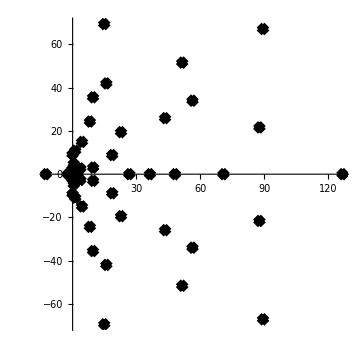

```mathematica
RootLocusPlot[1/Expand[EEc[100,x,1.1]],{k,0,1},FeedbackType->None]
```

```mathematica
Table[{n,Expand[Roots[EEc[n,x,2]==0,x]]},{n,41,64}]//TableForm
```

41 | x==Root[-120+174 #1-215 #1^2+65 #1^3-25 #1^4+#1^5&,1]||x==Root[-120+174 #1-215 #1^2+65 #1^3-25 #1^4+#1^5&,2]||x==Root[-120+174 #1-215 #1^2+65 #1^3-25 #1^4+#1^5&,3]||x==Root[-120+174 #1-215 #1^2+65 #1^3-25 #1^4+#1^5&,4]||x==Root[-120+174 #1-215 #1^2+65 #1^3-25 #1^4+#1^5&,5]
42 | x==6+1/2 √(1/3 (110+23473/(3511295+36 ⅈ √466050577)^(1/3)+(3511295+36 ⅈ √466050577)^(1/3)))-1/2 √(220/3-23473/(3 (3511295+36 ⅈ √466050577)^(1/3))-1/3 (3511295+36 ⅈ √466050577)^(1/3)-300/(√(1/3 (110+23473/(3511295+36 ⅈ √466050577)^(1/3)+(3511295+36 ⅈ √466050577)^(1/3)))))||x==6+1/2 √(1/3 (110+23473/(3511295+36 ⅈ √466050577)^(1/3)+(3511295+36 ⅈ √466050577)^(1/3)))+1/2 √(220/3-23473/(3 (3511295+36 ⅈ √466050577)^(1/3))-1/3 (3511295+36 ⅈ √466050577)^(1/3)-300/(√(1/3 (110+23473/(3511295+36 ⅈ √466050577)^(1/3)+(3511295+36 ⅈ √466050577)^(1/3)))))||x==6-1/2 √(1/3 (110+23473/(3511295+36 ⅈ √466050577)^(1/3)+(3511295+36 ⅈ √466050577)^(1/3)))-1/2 √(220/3-23473/(3 (3511295+36 ⅈ √466050577)^(1/3))-1/3 (3511295+36 ⅈ √466050577)^(1/3)+300/(√(1/3 (110+23473/(3511295+36 ⅈ √466050577)^(1/3)+(3511295+36 ⅈ √466050577)^(1/3)))))||x==6-1/2 √(1/3 (110+23473/(3511295+36 ⅈ √466050577)^(1/3)+(3511295+36 ⅈ √466050577)^(1/3)))+1/2 √(220/3-23473/(3 (3511295+36 ⅈ √466050577)^(1/3))-1/3 (3511295+36 ⅈ √466050577)^(1/3)+300/(√(1/3 (110+23473/(3511295+36 ⅈ √466050577)^(1/3)+(3511295+36 ⅈ √466050577)^(1/3)))))||x==1
43 | x==Root[-120+54 #1-215 #1^2+185 #1^3-25 #1^4+#1^5&,1]||x==Root[-120+54 #1-215 #1^2+185 #1^3-25 #1^4+#1^5&,2]||x==Root[-120+54 #1-215 #1^2+185 #1^3-25 #1^4+#1^5&,3]||x==Root[-120+54 #1-215 #1^2+185 #1^3-25 #1^4+#1^5&,4]||x==Root[-120+54 #1-215 #1^2+185 #1^3-25 #1^4+#1^5&,5]
44 | x==6-115/(√(3 (230+(2305835-36 √703377158)^(1/3)+(2305835+36 √703377158)^(1/3))))-(2305835-36 √703377158)^(1/3)/(2 √(3 (230+(2305835-36 √703377158)^(1/3)+(2305835+36 √703377158)^(1/3))))-(2305835+36 √703377158)^(1/3)/(2 √(3 (230+(2305835-36 √703377158)^(1/3)+(2305835+36 √703377158)^(1/3))))-1/2 √(460/3-1/3 (2305835-36 √703377158)^(1/3)-1/3 (2305835+36 √703377158)^(1/3)-900 √(3/(230+(2305835-36 √703377158)^(1/3)+(2305835+36 √703377158)^(1/3))))||x==6-115/(√(3 (230+(2305835-36 √703377158)^(1/3)+(2305835+36 √703377158)^(1/3))))-(2305835-36 √703377158)^(1/3)/(2 √(3 (230+(2305835-36 √703377158)^(1/3)+(2305835+36 √703377158)^(1/3))))-(2305835+36 √703377158)^(1/3)/(2 √(3 (230+(2305835-36 √703377158)^(1/3)+(2305835+36 √703377158)^(1/3))))+1/2 √(460/3-1/3 (2305835-36 √703377158)^(1/3)-1/3 (2305835+36 √703377158)^(1/3)-900 √(3/(230+(2305835-36 √703377158)^(1/3)+(2305835+36 √703377158)^(1/3))))||x==6+115/(√(3 (230+(2305835-36 √703377158)^(1/3)+(2305835+36 √703377158)^(1/3))))+(2305835-36 √703377158)^(1/3)/(2 √(3 (230+(2305835-36 √703377158)^(1/3)+(2305835+36 √703377158)^(1/3))))+(2305835+36 √703377158)^(1/3)/(2 √(3 (230+(2305835-36 √703377158)^(1/3)+(2305835+36 √703377158)^(1/3))))-1/2 √(460/3-1/3 (2305835-36 √703377158)^(1/3)-1/3 (2305835+36 √703377158)^(1/3)+900 √(3/(230+(2305835-36 √703377158)^(1/3)+(2305835+36 √703377158)^(1/3))))||x==6+115/(√(3 (230+(2305835-36 √703377158)^(1/3)+(2305835+36 √703377158)^(1/3))))+(2305835-36 √703377158)^(1/3)/(2 √(3 (230+(2305835-36 √703377158)^(1/3)+(2305835+36 √703377158)^(1/3))))+(2305835+36 √703377158)^(1/3)/(2 √(3 (230+(2305835-36 √703377158)^(1/3)+(2305835+36 √703377158)^(1/3))))+1/2 √(460/3-1/3 (2305835-36 √703377158)^(1/3)-1/3 (2305835+36 √703377158)^(1/3)+900 √(3/(230+(2305835-36 √703377158)^(1/3)+(2305835+36 √703377158)^(1/3))))||x==1
45 | x==Root[-120+54 #1-95 #1^2+65 #1^3-25 #1^4+#1^5&,1]||x==Root[-120+54 #1-95 #1^2+65 #1^3-25 #1^4+#1^5&,2]||x==Root[-120+54 #1-95 #1^2+65 #1^3-25 #1^4+#1^5&,3]||x==Root[-120+54 #1-95 #1^2+65 #1^3-25 #1^4+#1^5&,4]||x==Root[-120+54 #1-95 #1^2+65 #1^3-25 #1^4+#1^5&,5]
46 | x==6-175/(√(3 (350+(1175975-36 √690521723)^(1/3)+(1175975+36 √690521723)^(1/3))))-(1175975-36 √690521723)^(1/3)/(2 √(3 (350+(1175975-36 √690521723)^(1/3)+(1175975+36 √690521723)^(1/3))))-(1175975+36 √690521723)^(1/3)/(2 √(3 (350+(1175975-36 √690521723)^(1/3)+(1175975+36 √690521723)^(1/3))))-1/2 √(700/3-1/3 (1175975-36 √690521723)^(1/3)-1/3 (1175975+36 √690521723)^(1/3)-2340 √(3/(350+(1175975-36 √690521723)^(1/3)+(1175975+36 √690521723)^(1/3))))||x==6-175/(√(3 (350+(1175975-36 √690521723)^(1/3)+(1175975+36 √690521723)^(1/3))))-(1175975-36 √690521723)^(1/3)/(2 √(3 (350+(1175975-36 √690521723)^(1/3)+(1175975+36 √690521723)^(1/3))))-(1175975+36 √690521723)^(1/3)/(2 √(3 (350+(1175975-36 √690521723)^(1/3)+(1175975+36 √690521723)^(1/3))))+1/2 √(700/3-1/3 (1175975-36 √690521723)^(1/3)-1/3 (1175975+36 √690521723)^(1/3)-2340 √(3/(350+(1175975-36 √690521723)^(1/3)+(1175975+36 √690521723)^(1/3))))||x==6+175/(√(3 (350+(1175975-36 √690521723)^(1/3)+(1175975+36 √690521723)^(1/3))))+(1175975-36 √690521723)^(1/3)/(2 √(3 (350+(1175975-36 √690521723)^(1/3)+(1175975+36 √690521723)^(1/3))))+(1175975+36 √690521723)^(1/3)/(2 √(3 (350+(1175975-36 √690521723)^(1/3)+(1175975+36 √690521723)^(1/3))))-1/2 √(700/3-1/3 (1175975-36 √690521723)^(1/3)-1/3 (1175975+36 √690521723)^(1/3)+2340 √(3/(350+(1175975-36 √690521723)^(1/3)+(1175975+36 √690521723)^(1/3))))||x==6+175/(√(3 (350+(1175975-36 √690521723)^(1/3)+(1175975+36 √690521723)^(1/3))))+(1175975-36 √690521723)^(1/3)/(2 √(3 (350+(1175975-36 √690521723)^(1/3)+(1175975+36 √690521723)^(1/3))))+(1175975+36 √690521723)^(1/3)/(2 √(3 (350+(1175975-36 √690521723)^(1/3)+(1175975+36 √690521723)^(1/3))))+1/2 √(700/3-1/3 (1175975-36 √690521723)^(1/3)-1/3 (1175975+36 √690521723)^(1/3)+2340 √(3/(350+(1175975-36 √690521723)^(1/3)+(1175975+36 √690521723)^(1/3))))||x==1
47 | x==23/4-1435/(4 √(3 (1435+4 (571780-828 √243597)^(1/3)+4 2^(2/3) (23 (6215+9 √243597))^(1/3))))-(571780-828 √243597)^(1/3)/(√(3 (1435+4 (571780-828 √243597)^(1/3)+4 2^(2/3) (23 (6215+9 √243597))^(1/3))))-(2^(2/3) (23 (6215+9 √243597))^(1/3))/(√(3 (1435+4 (571780-828 √243597)^(1/3)+4 2^(2/3) (23 (6215+9 √243597))^(1/3))))-1/2 √(1435/6-1/3 (571780-828 √243597)^(1/3)-1/3 2^(2/3) (23 (6215+9 √243597))^(1/3)-9915/2 √(3/(1435+4 (571780-828 √243597)^(1/3)+4 2^(2/3) (23 (6215+9 √243597))^(1/3))))||x==23/4-1435/(4 √(3 (1435+4 (571780-828 √243597)^(1/3)+4 2^(2/3) (23 (6215+9 √243597))^(1/3))))-(571780-828 √243597)^(1/3)/(√(3 (1435+4 (571780-828 √243597)^(1/3)+4 2^(2/3) (23 (6215+9 √243597))^(1/3))))-(2^(2/3) (23 (6215+9 √243597))^(1/3))/(√(3 (1435+4 (571780-828 √243597)^(1/3)+4 2^(2/3) (23 (6215+9 √243597))^(1/3))))+1/2 √(1435/6-1/3 (571780-828 √243597)^(1/3)-1/3 2^(2/3) (23 (6215+9 √243597))^(1/3)-9915/2 √(3/(1435+4 (571780-828 √243597)^(1/3)+4 2^(2/3) (23 (6215+9 √243597))^(1/3))))||x==23/4+1435/(4 √(3 (1435+4 (571780-828 √243597)^(1/3)+4 2^(2/3) (23 (6215+9 √243597))^(1/3))))+(571780-828 √243597)^(1/3)/(√(3 (1435+4 (571780-828 √243597)^(1/3)+4 2^(2/3) (23 (6215+9 √243597))^(1/3))))+(2^(2/3) (23 (6215+9 √243597))^(1/3))/(√(3 (1435+4 (571780-828 √243597)^(1/3)+4 2^(2/3) (23 (6215+9 √243597))^(1/3))))-1/2 √(1435/6-1/3 (571780-828 √243597)^(1/3)-1/3 2^(2/3) (23 (6215+9 √243597))^(1/3)+9915/2 √(3/(1435+4 (571780-828 √243597)^(1/3)+4 2^(2/3) (23 (6215+9 √243597))^(1/3))))||x==23/4+1435/(4 √(3 (1435+4 (571780-828 √243597)^(1/3)+4 2^(2/3) (23 (6215+9 √243597))^(1/3))))+(571780-828 √243597)^(1/3)/(√(3 (1435+4 (571780-828 √243597)^(1/3)+4 2^(2/3) (23 (6215+9 √243597))^(1/3))))+(2^(2/3) (23 (6215+9 √243597))^(1/3))/(√(3 (1435+4 (571780-828 √243597)^(1/3)+4 2^(2/3) (23 (6215+9 √243597))^(1/3))))+1/2 √(1435/6-1/3 (571780-828 √243597)^(1/3)-1/3 2^(2/3) (23 (6215+9 √243597))^(1/3)+9915/2 √(3/(1435+4 (571780-828 √243597)^(1/3)+4 2^(2/3) (23 (6215+9 √243597))^(1/3))))||x==2
48 | x==61/16+1915/(16 √(3 (1915+16 (10216180-9 √256605466893)^(1/3)+16 (10216180+9 √256605466893)^(1/3))))+(10216180-9 √256605466893)^(1/3)/(√(3 (1915+16 (10216180-9 √256605466893)^(1/3)+16 (10216180+9 √256605466893)^(1/3))))+(10216180+9 √256605466893)^(1/3)/(√(3 (1915+16 (10216180-9 √256605466893)^(1/3)+16 (10216180+9 √256605466893)^(1/3))))-1/2 √(1915/96-1/12 (10216180-9 √256605466893)^(1/3)-1/12 (10216180+9 √256605466893)^(1/3)-31275/32 √(3/(1915+16 (10216180-9 √256605466893)^(1/3)+16 (10216180+9 √256605466893)^(1/3))))||x==61/16+1915/(16 √(3 (1915+16 (10216180-9 √256605466893)^(1/3)+16 (10216180+9 √256605466893)^(1/3))))+(10216180-9 √256605466893)^(1/3)/(√(3 (1915+16 (10216180-9 √256605466893)^(1/3)+16 (10216180+9 √256605466893)^(1/3))))+(10216180+9 √256605466893)^(1/3)/(√(3 (1915+16 (10216180-9 √256605466893)^(1/3)+16 (10216180+9 √256605466893)^(1/3))))+1/2 √(1915/96-1/12 (10216180-9 √256605466893)^(1/3)-1/12 (10216180+9 √256605466893)^(1/3)-31275/32 √(3/(1915+16 (10216180-9 √256605466893)^(1/3)+16 (10216180+9 √256605466893)^(1/3))))||x==61/16-1915/(16 √(3 (1915+16 (10216180-9 √256605466893)^(1/3)+16 (10216180+9 √256605466893)^(1/3))))-(10216180-9 √256605466893)^(1/3)/(√(3 (1915+16 (10216180-9 √256605466893)^(1/3)+16 (10216180+9 √256605466893)^(1/3))))-(10216180+9 √256605466893)^(1/3)/(√(3 (1915+16 (10216180-9 √256605466893)^(1/3)+16 (10216180+9 √256605466893)^(1/3))))-1/2 √(1915/96-1/12 (10216180-9 √256605466893)^(1/3)-1/12 (10216180+9 √256605466893)^(1/3)+31275/32 √(3/(1915+16 (10216180-9 √256605466893)^(1/3)+16 (10216180+9 √256605466893)^(1/3))))||x==61/16-1915/(16 √(3 (1915+16 (10216180-9 √256605466893)^(1/3)+16 (10216180+9 √256605466893)^(1/3))))-(10216180-9 √256605466893)^(1/3)/(√(3 (1915+16 (10216180-9 √256605466893)^(1/3)+16 (10216180+9 √256605466893)^(1/3))))-(10216180+9 √256605466893)^(1/3)/(√(3 (1915+16 (10216180-9 √256605466893)^(1/3)+16 (10216180+9 √256605466893)^(1/3))))+1/2 √(1915/96-1/12 (10216180-9 √256605466893)^(1/3)-1/12 (10216180+9 √256605466893)^(1/3)+31275/32 √(3/(1915+16 (10216180-9 √256605466893)^(1/3)+16 (10216180+9 √256605466893)^(1/3))))||x==1
49 | x==Root[120+126 #1-415 #1^2+350 #1^3-65 #1^4+4 #1^5&,1]||x==Root[120+126 #1-415 #1^2+350 #1^3-65 #1^4+4 #1^5&,2]||x==Root[120+126 #1-415 #1^2+350 #1^3-65 #1^4+4 #1^5&,3]||x==Root[120+126 #1-415 #1^2+350 #1^3-65 #1^4+4 #1^5&,4]||x==Root[120+126 #1-415 #1^2+350 #1^3-65 #1^4+4 #1^5&,5]
50 | x==61/16-3835/(16 √(3 (3835-26608/(2257730-9 √62873402613)^(1/3)-16 (2257730-9 √62873402613)^(1/3))))+1663/((2257730-9 √62873402613)^(1/3) √(3 (3835-26608/(2257730-9 √62873402613)^(1/3)-16 (2257730-9 √62873402613)^(1/3))))+(2257730-9 √62873402613)^(1/3)/(√(3 (3835-26608/(2257730-9 √62873402613)^(1/3)-16 (2257730-9 √62873402613)^(1/3))))-1/2 √(3835/96+1663/(12 (2257730-9 √62873402613)^(1/3))+1/12 (2257730-9 √62873402613)^(1/3)-34965/32 √(3/(3835-26608/(2257730-9 √62873402613)^(1/3)-16 (2257730-9 √62873402613)^(1/3))))||x==61/16-3835/(16 √(3 (3835-26608/(2257730-9 √62873402613)^(1/3)-16 (2257730-9 √62873402613)^(1/3))))+1663/((2257730-9 √62873402613)^(1/3) √(3 (3835-26608/(2257730-9 √62873402613)^(1/3)-16 (2257730-9 √62873402613)^(1/3))))+(2257730-9 √62873402613)^(1/3)/(√(3 (3835-26608/(2257730-9 √62873402613)^(1/3)-16 (2257730-9 √62873402613)^(1/3))))+1/2 √(3835/96+1663/(12 (2257730-9 √62873402613)^(1/3))+1/12 (2257730-9 √62873402613)^(1/3)-34965/32 √(3/(3835-26608/(2257730-9 √62873402613)^(1/3)-16 (2257730-9 √62873402613)^(1/3))))||x==61/16+3835/(16 √(3 (3835-26608/(2257730-9 √62873402613)^(1/3)-16 (2257730-9 √62873402613)^(1/3))))-1663/((2257730-9 √62873402613)^(1/3) √(3 (3835-26608/(2257730-9 √62873402613)^(1/3)-16 (2257730-9 √62873402613)^(1/3))))-(2257730-9 √62873402613)^(1/3)/(√(3 (3835-26608/(2257730-9 √62873402613)^(1/3)-16 (2257730-9 √62873402613)^(1/3))))-1/2 √(3835/96+1663/(12 (2257730-9 √62873402613)^(1/3))+1/12 (2257730-9 √62873402613)^(1/3)+34965/32 √(3/(3835-26608/(2257730-9 √62873402613)^(1/3)-16 (2257730-9 √62873402613)^(1/3))))||x==61/16+3835/(16 √(3 (3835-26608/(2257730-9 √62873402613)^(1/3)-16 (2257730-9 √62873402613)^(1/3))))-1663/((2257730-9 √62873402613)^(1/3) √(3 (3835-26608/(2257730-9 √62873402613)^(1/3)-16 (2257730-9 √62873402613)^(1/3))))-(2257730-9 √62873402613)^(1/3)/(√(3 (3835-26608/(2257730-9 √62873402613)^(1/3)-16 (2257730-9 √62873402613)^(1/3))))+1/2 √(3835/96+1663/(12 (2257730-9 √62873402613)^(1/3))+1/12 (2257730-9 √62873402613)^(1/3)+34965/32 √(3/(3835-26608/(2257730-9 √62873402613)^(1/3)-16 (2257730-9 √62873402613)^(1/3))))||x==1
51 | x==45/16-3995/(16 √(3 (3995-15632/(-503110+9 √3136447493)^(1/3)+16 (-503110+9 √3136447493)^(1/3))))+977/((-503110+9 √3136447493)^(1/3) √(3 (3995-15632/(-503110+9 √3136447493)^(1/3)+16 (-503110+9 √3136447493)^(1/3))))-(-503110+9 √3136447493)^(1/3)/(√(3 (3995-15632/(-503110+9 √3136447493)^(1/3)+16 (-503110+9 √3136447493)^(1/3))))-1/2 √(3995/96+977/(12 (-503110+9 √3136447493)^(1/3))-1/12 (-503110+9 √3136447493)^(1/3)-48165/32 √(3/(3995-15632/(-503110+9 √3136447493)^(1/3)+16 (-503110+9 √3136447493)^(1/3))))||x==45/16-3995/(16 √(3 (3995-15632/(-503110+9 √3136447493)^(1/3)+16 (-503110+9 √3136447493)^(1/3))))+977/((-503110+9 √3136447493)^(1/3) √(3 (3995-15632/(-503110+9 √3136447493)^(1/3)+16 (-503110+9 √3136447493)^(1/3))))-(-503110+9 √3136447493)^(1/3)/(√(3 (3995-15632/(-503110+9 √3136447493)^(1/3)+16 (-503110+9 √3136447493)^(1/3))))+1/2 √(3995/96+977/(12 (-503110+9 √3136447493)^(1/3))-1/12 (-503110+9 √3136447493)^(1/3)-48165/32 √(3/(3995-15632/(-503110+9 √3136447493)^(1/3)+16 (-503110+9 √3136447493)^(1/3))))||x==45/16+3995/(16 √(3 (3995-15632/(-503110+9 √3136447493)^(1/3)+16 (-503110+9 √3136447493)^(1/3))))-977/((-503110+9 √3136447493)^(1/3) √(3 (3995-15632/(-503110+9 √3136447493)^(1/3)+16 (-503110+9 √3136447493)^(1/3))))+(-503110+9 √3136447493)^(1/3)/(√(3 (3995-15632/(-503110+9 √3136447493)^(1/3)+16 (-503110+9 √3136447493)^(1/3))))-1/2 √(3995/96+977/(12 (-503110+9 √3136447493)^(1/3))-1/12 (-503110+9 √3136447493)^(1/3)+48165/32 √(3/(3995-15632/(-503110+9 √3136447493)^(1/3)+16 (-503110+9 √3136447493)^(1/3))))||x==45/16+3995/(16 √(3 (3995-15632/(-503110+9 √3136447493)^(1/3)+16 (-503110+9 √3136447493)^(1/3))))-977/((-503110+9 √3136447493)^(1/3) √(3 (3995-15632/(-503110+9 √3136447493)^(1/3)+16 (-503110+9 √3136447493)^(1/3))))+(-503110+9 √3136447493)^(1/3)/(√(3 (3995-15632/(-503110+9 √3136447493)^(1/3)+16 (-503110+9 √3136447493)^(1/3))))+1/2 √(3995/96+977/(12 (-503110+9 √3136447493)^(1/3))-1/12 (-503110+9 √3136447493)^(1/3)+48165/32 √(3/(3995-15632/(-503110+9 √3136447493)^(1/3)+16 (-503110+9 √3136447493)^(1/3))))||x==5
52 | x==61/16+1915/(16 √(3 (1915+16 (6856030-117 √869402037)^(1/3)+16 (6856030+117 √869402037)^(1/3))))+(6856030-117 √869402037)^(1/3)/(√(3 (1915+16 (6856030-117 √869402037)^(1/3)+16 (6856030+117 √869402037)^(1/3))))+(6856030+117 √869402037)^(1/3)/(√(3 (1915+16 (6856030-117 √869402037)^(1/3)+16 (6856030+117 √869402037)^(1/3))))-1/2 √(1915/96-1/12 (6856030-117 √869402037)^(1/3)-1/12 (6856030+117 √869402037)^(1/3)-23595/32 √(3/(1915+16 (6856030-117 √869402037)^(1/3)+16 (6856030+117 √869402037)^(1/3))))||x==61/16+1915/(16 √(3 (1915+16 (6856030-117 √869402037)^(1/3)+16 (6856030+117 √869402037)^(1/3))))+(6856030-117 √869402037)^(1/3)/(√(3 (1915+16 (6856030-117 √869402037)^(1/3)+16 (6856030+117 √869402037)^(1/3))))+(6856030+117 √869402037)^(1/3)/(√(3 (1915+16 (6856030-117 √869402037)^(1/3)+16 (6856030+117 √869402037)^(1/3))))+1/2 √(1915/96-1/12 (6856030-117 √869402037)^(1/3)-1/12 (6856030+117 √869402037)^(1/3)-23595/32 √(3/(1915+16 (6856030-117 √869402037)^(1/3)+16 (6856030+117 √869402037)^(1/3))))||x==61/16-1915/(16 √(3 (1915+16 (6856030-117 √869402037)^(1/3)+16 (6856030+117 √869402037)^(1/3))))-(6856030-117 √869402037)^(1/3)/(√(3 (1915+16 (6856030-117 √869402037)^(1/3)+16 (6856030+117 √869402037)^(1/3))))-(6856030+117 √869402037)^(1/3)/(√(3 (1915+16 (6856030-117 √869402037)^(1/3)+16 (6856030+117 √869402037)^(1/3))))-1/2 √(1915/96-1/12 (6856030-117 √869402037)^(1/3)-1/12 (6856030+117 √869402037)^(1/3)+23595/32 √(3/(1915+16 (6856030-117 √869402037)^(1/3)+16 (6856030+117 √869402037)^(1/3))))||x==61/16-1915/(16 √(3 (1915+16 (6856030-117 √869402037)^(1/3)+16 (6856030+117 √869402037)^(1/3))))-(6856030-117 √869402037)^(1/3)/(√(3 (1915+16 (6856030-117 √869402037)^(1/3)+16 (6856030+117 √869402037)^(1/3))))-(6856030+117 √869402037)^(1/3)/(√(3 (1915+16 (6856030-117 √869402037)^(1/3)+16 (6856030+117 √869402037)^(1/3))))+1/2 √(1915/96-1/12 (6856030-117 √869402037)^(1/3)-1/12 (6856030+117 √869402037)^(1/3)+23595/32 √(3/(1915+16 (6856030-117 √869402037)^(1/3)+16 (6856030+117 √869402037)^(1/3))))||x==1
53 | x==Root[120+246 #1-535 #1^2+350 #1^3-65 #1^4+4 #1^5&,1]||x==Root[120+246 #1-535 #1^2+350 #1^3-65 #1^4+4 #1^5&,2]||x==Root[120+246 #1-535 #1^2+350 #1^3-65 #1^4+4 #1^5&,3]||x==Root[120+246 #1-535 #1^2+350 #1^3-65 #1^4+4 #1^5&,4]||x==Root[120+246 #1-535 #1^2+350 #1^3-65 #1^4+4 #1^5&,5]
54 | x==81/16-12995/(16 √(3 (12995-816272/(-18536410+9 √5881261616173)^(1/3)+16 (-18536410+9 √5881261616173)^(1/3))))+51017/((-18536410+9 √5881261616173)^(1/3) √(3 (12995-816272/(-18536410+9 √5881261616173)^(1/3)+16 (-18536410+9 √5881261616173)^(1/3))))-(-18536410+9 √5881261616173)^(1/3)/(√(3 (12995-816272/(-18536410+9 √5881261616173)^(1/3)+16 (-18536410+9 √5881261616173)^(1/3))))-1/2 √(12995/96+51017/(12 (-18536410+9 √5881261616173)^(1/3))-1/12 (-18536410+9 √5881261616173)^(1/3)-307425/32 √(3/(12995-816272/(-18536410+9 √5881261616173)^(1/3)+16 (-18536410+9 √5881261616173)^(1/3))))||x==81/16-12995/(16 √(3 (12995-816272/(-18536410+9 √5881261616173)^(1/3)+16 (-18536410+9 √5881261616173)^(1/3))))+51017/((-18536410+9 √5881261616173)^(1/3) √(3 (12995-816272/(-18536410+9 √5881261616173)^(1/3)+16 (-18536410+9 √5881261616173)^(1/3))))-(-18536410+9 √5881261616173)^(1/3)/(√(3 (12995-816272/(-18536410+9 √5881261616173)^(1/3)+16 (-18536410+9 √5881261616173)^(1/3))))+1/2 √(12995/96+51017/(12 (-18536410+9 √5881261616173)^(1/3))-1/12 (-18536410+9 √5881261616173)^(1/3)-307425/32 √(3/(12995-816272/(-18536410+9 √5881261616173)^(1/3)+16 (-18536410+9 √5881261616173)^(1/3))))||x==81/16+12995/(16 √(3 (12995-816272/(-18536410+9 √5881261616173)^(1/3)+16 (-18536410+9 √5881261616173)^(1/3))))-51017/((-18536410+9 √5881261616173)^(1/3) √(3 (12995-816272/(-18536410+9 √5881261616173)^(1/3)+16 (-18536410+9 √5881261616173)^(1/3))))+(-18536410+9 √5881261616173)^(1/3)/(√(3 (12995-816272/(-18536410+9 √5881261616173)^(1/3)+16 (-18536410+9 √5881261616173)^(1/3))))-1/2 √(12995/96+51017/(12 (-18536410+9 √5881261616173)^(1/3))-1/12 (-18536410+9 √5881261616173)^(1/3)+307425/32 √(3/(12995-816272/(-18536410+9 √5881261616173)^(1/3)+16 (-18536410+9 √5881261616173)^(1/3))))||x==81/16+12995/(16 √(3 (12995-816272/(-18536410+9 √5881261616173)^(1/3)+16 (-18536410+9 √5881261616173)^(1/3))))-51017/((-18536410+9 √5881261616173)^(1/3) √(3 (12995-816272/(-18536410+9 √5881261616173)^(1/3)+16 (-18536410+9 √5881261616173)^(1/3))))+(-18536410+9 √5881261616173)^(1/3)/(√(3 (12995-816272/(-18536410+9 √5881261616173)^(1/3)+16 (-18536410+9 √5881261616173)^(1/3))))+1/2 √(12995/96+51017/(12 (-18536410+9 √5881261616173)^(1/3))-1/12 (-18536410+9 √5881261616173)^(1/3)+307425/32 √(3/(12995-816272/(-18536410+9 √5881261616173)^(1/3)+16 (-18536410+9 √5881261616173)^(1/3))))||x==1
55 | x==Root[120+246 #1-455 #1^2+290 #1^3-85 #1^4+4 #1^5&,1]||x==Root[120+246 #1-455 #1^2+290 #1^3-85 #1^4+4 #1^5&,2]||x==Root[120+246 #1-455 #1^2+290 #1^3-85 #1^4+4 #1^5&,3]||x==Root[120+246 #1-455 #1^2+290 #1^3-85 #1^4+4 #1^5&,4]||x==Root[120+246 #1-455 #1^2+290 #1^3-85 #1^4+4 #1^5&,5]
56 | x==101/16-1/16 √(6265-34672/(520530-√260775489437)^(1/3)-16 (520530-√260775489437)^(1/3))-1/2 √(6265/32+2167/(4 (520530-√260775489437)^(1/3))+1/4 (520530-√260775489437)^(1/3)-480845/(32 √(6265-34672/(520530-√260775489437)^(1/3)-16 (520530-√260775489437)^(1/3))))||x==101/16-1/16 √(6265-34672/(520530-√260775489437)^(1/3)-16 (520530-√260775489437)^(1/3))+1/2 √(6265/32+2167/(4 (520530-√260775489437)^(1/3))+1/4 (520530-√260775489437)^(1/3)-480845/(32 √(6265-34672/(520530-√260775489437)^(1/3)-16 (520530-√260775489437)^(1/3))))||x==101/16+1/16 √(6265-34672/(520530-√260775489437)^(1/3)-16 (520530-√260775489437)^(1/3))-1/2 √(6265/32+2167/(4 (520530-√260775489437)^(1/3))+1/4 (520530-√260775489437)^(1/3)+480845/(32 √(6265-34672/(520530-√260775489437)^(1/3)-16 (520530-√260775489437)^(1/3))))||x==101/16+1/16 √(6265-34672/(520530-√260775489437)^(1/3)-16 (520530-√260775489437)^(1/3))+1/2 √(6265/32+2167/(4 (520530-√260775489437)^(1/3))+1/4 (520530-√260775489437)^(1/3)+480845/(32 √(6265-34672/(520530-√260775489437)^(1/3)-16 (520530-√260775489437)^(1/3))))||x==1
57 | x==Root[120+246 #1-615 #1^2+470 #1^3-105 #1^4+4 #1^5&,1]||x==Root[120+246 #1-615 #1^2+470 #1^3-105 #1^4+4 #1^5&,2]||x==Root[120+246 #1-615 #1^2+470 #1^3-105 #1^4+4 #1^5&,3]||x==Root[120+246 #1-615 #1^2+470 #1^3-105 #1^4+4 #1^5&,4]||x==Root[120+246 #1-615 #1^2+470 #1^3-105 #1^4+4 #1^5&,5]
58 | x==101/16-1/16 √(6265-34672/(520530-√260775489437)^(1/3)-16 (520530-√260775489437)^(1/3))-1/2 √(6265/32+2167/(4 (520530-√260775489437)^(1/3))+1/4 (520530-√260775489437)^(1/3)-480845/(32 √(6265-34672/(520530-√260775489437)^(1/3)-16 (520530-√260775489437)^(1/3))))||x==101/16-1/16 √(6265-34672/(520530-√260775489437)^(1/3)-16 (520530-√260775489437)^(1/3))+1/2 √(6265/32+2167/(4 (520530-√260775489437)^(1/3))+1/4 (520530-√260775489437)^(1/3)-480845/(32 √(6265-34672/(520530-√260775489437)^(1/3)-16 (520530-√260775489437)^(1/3))))||x==101/16+1/16 √(6265-34672/(520530-√260775489437)^(1/3)-16 (520530-√260775489437)^(1/3))-1/2 √(6265/32+2167/(4 (520530-√260775489437)^(1/3))+1/4 (520530-√260775489437)^(1/3)+480845/(32 √(6265-34672/(520530-√260775489437)^(1/3)-16 (520530-√260775489437)^(1/3))))||x==101/16+1/16 √(6265-34672/(520530-√260775489437)^(1/3)-16 (520530-√260775489437)^(1/3))+1/2 √(6265/32+2167/(4 (520530-√260775489437)^(1/3))+1/4 (520530-√260775489437)^(1/3)+480845/(32 √(6265-34672/(520530-√260775489437)^(1/3)-16 (520530-√260775489437)^(1/3))))||x==1
59 | x==Root[120+366 #1-735 #1^2+470 #1^3-105 #1^4+4 #1^5&,1]||x==Root[120+366 #1-735 #1^2+470 #1^3-105 #1^4+4 #1^5&,2]||x==Root[120+366 #1-735 #1^2+470 #1^3-105 #1^4+4 #1^5&,3]||x==Root[120+366 #1-735 #1^2+470 #1^3-105 #1^4+4 #1^5&,4]||x==Root[120+366 #1-735 #1^2+470 #1^3-105 #1^4+4 #1^5&,5]
60 | x==41/16+1/16 √(-975-6288/(275750+√76098760957)^(1/3)+16 (275750+√76098760957)^(1/3))-1/2 √(-975/32+393/(4 (275750+√76098760957)^(1/3))-1/4 (275750+√76098760957)^(1/3)-32215/(32 √(-975-6288/(275750+√76098760957)^(1/3)+16 (275750+√76098760957)^(1/3))))||x==41/16+1/16 √(-975-6288/(275750+√76098760957)^(1/3)+16 (275750+√76098760957)^(1/3))+1/2 √(-975/32+393/(4 (275750+√76098760957)^(1/3))-1/4 (275750+√76098760957)^(1/3)-32215/(32 √(-975-6288/(275750+√76098760957)^(1/3)+16 (275750+√76098760957)^(1/3))))||x==41/16-1/16 √(-975-6288/(275750+√76098760957)^(1/3)+16 (275750+√76098760957)^(1/3))-1/2 √(-975/32+393/(4 (275750+√76098760957)^(1/3))-1/4 (275750+√76098760957)^(1/3)+32215/(32 √(-975-6288/(275750+√76098760957)^(1/3)+16 (275750+√76098760957)^(1/3))))||x==41/16-1/16 √(-975-6288/(275750+√76098760957)^(1/3)+16 (275750+√76098760957)^(1/3))+1/2 √(-975/32+393/(4 (275750+√76098760957)^(1/3))-1/4 (275750+√76098760957)^(1/3)+32215/(32 √(-975-6288/(275750+√76098760957)^(1/3)+16 (275750+√76098760957)^(1/3))))||x==1
61 | x==Root[120+486 #1-735 #1^2+290 #1^3-45 #1^4+4 #1^5&,1]||x==Root[120+486 #1-735 #1^2+290 #1^3-45 #1^4+4 #1^5&,2]||x==Root[120+486 #1-735 #1^2+290 #1^3-45 #1^4+4 #1^5&,3]||x==Root[120+486 #1-735 #1^2+290 #1^3-45 #1^4+4 #1^5&,4]||x==Root[120+486 #1-735 #1^2+290 #1^3-45 #1^4+4 #1^5&,5]
62 | x==41/16+1/16 √(-975-32528/(333650+√119724892437)^(1/3)+16 (333650+√119724892437)^(1/3))-1/2 √(-975/32+2033/(4 (333650+√119724892437)^(1/3))-1/4 (333650+√119724892437)^(1/3)-16855/(32 √(-975-32528/(333650+√119724892437)^(1/3)+16 (333650+√119724892437)^(1/3))))||x==41/16+1/16 √(-975-32528/(333650+√119724892437)^(1/3)+16 (333650+√119724892437)^(1/3))+1/2 √(-975/32+2033/(4 (333650+√119724892437)^(1/3))-1/4 (333650+√119724892437)^(1/3)-16855/(32 √(-975-32528/(333650+√119724892437)^(1/3)+16 (333650+√119724892437)^(1/3))))||x==41/16-1/16 √(-975-32528/(333650+√119724892437)^(1/3)+16 (333650+√119724892437)^(1/3))-1/2 √(-975/32+2033/(4 (333650+√119724892437)^(1/3))-1/4 (333650+√119724892437)^(1/3)+16855/(32 √(-975-32528/(333650+√119724892437)^(1/3)+16 (333650+√119724892437)^(1/3))))||x==41/16-1/16 √(-975-32528/(333650+√119724892437)^(1/3)+16 (333650+√119724892437)^(1/3))+1/2 √(-975/32+2033/(4 (333650+√119724892437)^(1/3))-1/4 (333650+√119724892437)^(1/3)+16855/(32 √(-975-32528/(333650+√119724892437)^(1/3)+16 (333650+√119724892437)^(1/3))))||x==1
63 | x==Root[120+486 #1-795 #1^2+350 #1^3-45 #1^4+4 #1^5&,1]||x==Root[120+486 #1-795 #1^2+350 #1^3-45 #1^4+4 #1^5&,2]||x==Root[120+486 #1-795 #1^2+350 #1^3-45 #1^4+4 #1^5&,3]||x==Root[120+486 #1-795 #1^2+350 #1^3-45 #1^4+4 #1^5&,4]||x==Root[120+486 #1-795 #1^2+350 #1^3-45 #1^4+4 #1^5&,5]
64 | x==Root[-720+3924 #1-1780 #1^2+395 #1^3-20 #1^4+#1^5&,1]||x==Root[-720+3924 #1-1780 #1^2+395 #1^3-20 #1^4+#1^5&,2]||x==Root[-720+3924 #1-1780 #1^2+395 #1^3-20 #1^4+#1^5&,3]||x==Root[-720+3924 #1-1780 #1^2+395 #1^3-20 #1^4+#1^5&,4]||x==Root[-720+3924 #1-1780 #1^2+395 #1^3-20 #1^4+#1^5&,5]||x==1

```mathematica
EE1[n_,z_,b_]:=Sum[FactorialPower[z,a]/a! (E2a[n,a,b])/z+1/a,{a,1,Log[If[b>2,2,b],n]}]
Limit[( EE1[100,z,2]),{z->0}]+Sum[ ((2)^k-1)/k,{k,1,Log[2,100]}]
```

{428/15}

```mathematica
EE1a[n_,z_,b_]:=Sum[FactorialPower[z,a]/a! (E2aa[n,a,b])/z+1/a,{a,1,Log[If[b>2,2,b],n]}]
```

```mathematica
Expand[Limit[( EE1a[100,z,2]),{z->0}]]
```

{49/20+E2aa[100,1,2]-1/2 E2aa[100,2,2]+1/3 E2aa[100,3,2]-1/4 E2aa[100,4,2]+1/5 E2aa[100,5,2]-1/6 E2aa[100,6,2]}

```mathematica
EE1b[n_,z_,b_]:=Sum[bins[z,a]E2a[n,a,b]/z+1/a,{a,1,Log[If[b>2,2,b],n]}]
Limit[( EE1b[100,z,2]),{z->0}]+Sum[ ((2)^k-1)/k,{k,1,Log[2,100]}]
```

{428/15}

```mathematica
(1-2/List@@NRoots[EEc[94,x,2]==0,x][[All,2]])
```

{2.10101-1.89751 ⅈ,2.10101+1.89751 ⅈ,-1.,0.720918-0.364325 ⅈ,0.720918+0.364325 ⅈ,0.956155}

```mathematica
EEc[100,1,2]
```

0

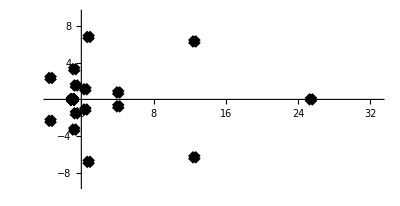

```mathematica
RootLocusPlot[1/Expand[gg[20,x,1.1]],{k,0,1},FeedbackType->None]
```

```mathematica
EEc[ 99,1,2]
```

1

```mathematica
(-1/List@@NRoots[gg[101,x,2]==0,x][[All,2]])
```

Power::infy: Infinite expression 1/0. encountered.

{2.25303,ComplexInfinity,-0.376268,-0.0861804-0.0429715 ⅈ,-0.0861804+0.0429715 ⅈ}

```mathematica
ff[z_] := z(n-1)(1-(z-1)/a)(1-(z-1)/b)(1-(z-1)/c)(1-(z-1)/d)(1-(z-1)/e)
ffp[z_] := (n-1)(1+1/a)(1+1/b)(1+1/c)(1+1/d)(1+1/e)
```

```mathematica
FullSimplify[Expand[ff[p]]/Expand[ff[q]]]
```

((1+a-p) (1+b-p) (1+c-p) (1+d-p) (1+e-p) p)/((1+a-q) q (-1-b+q) (-1-c+q) (-1-d+q) (-1-e+q))

```mathematica
FullSimplify[ff[p]/ff[q]]
```

((1+a-p) p (-1-b+p) (-1-c+p) (-1-d+p) (-1-e+p))/((1+a-q) q (-1-b+q) (-1-c+q) (-1-d+q) (-1-e+q))

```mathematica
FullSimplify[ff[2]/ffp[q]]
```

(2 (-1+a) (-1+b) (-1+c) (-1+d) (-1+e))/((1+a) (1+b) (1+c) (1+d) (1+e))

```mathematica
FullSimplify[ff[-1]/ffp[q]]
```

-((2+a) (2+b) (2+c) (2+d) (2+e))/((1+a) (1+b) (1+c) (1+d) (1+e))

```mathematica
FullSimplify[ff[5]/ff[2]]
```

(5 (-4+a) (-4+b) (-4+c) (-4+d) (-4+e))/(2 (-1+a) (-1+b) (-1+c) (-1+d) (-1+e))

```mathematica
FullSimplify[ff[2]/ffp[q]]
```

(2 (-1+a) (-1+b) (-1+c) (-1+d) (-1+e))/((1+a) (1+b) (1+c) (1+d) (1+e))